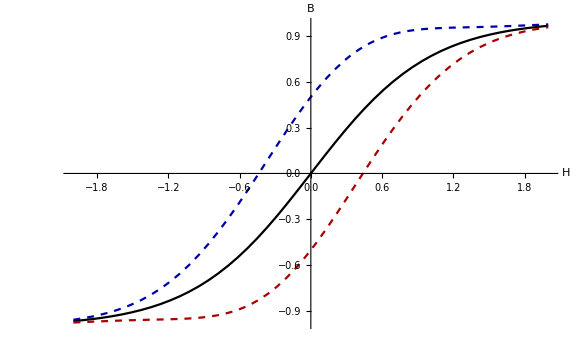

```mathematica
Plot[{Style[Tanh[x],Black],Style[Tanh[x]+E^(-x^2)/2,{Dashed,Blue//Darker}],Style[Tanh[x]-E^(-x^2)/2,{Dashed,Red//Darker}]},{x,-2,2},AxesLabel->{"H","B"},Ticks->None,LabelStyle->{Black,FontFamily->"CMU Sans Serif",FontSize->22}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<MeshTools.wl
```

```mathematica
outerDiameter=10/100;
outerShellThickness=1/100;
rotorInnerDiameter=1.5/100;
rotorOuterDiameter=4.5/100;
numCoils=6;
rotorStatorDistance=.25/100;
coilInnerDiameter=3.5/100;
coilOuterDiameter=coilInnerDiameter*1.4;
coilInnerOffset=0.3/100;
coilOuterOffset=0.4/100;
offsetCoils=1/2;
coilColor=Darker[Darker[Gray]];
rotorColor=Darker[Red//Darker];
statorColor=Black;
```

/Users/tomginsberg/Documents/School/phys/pms/motorsim/

```mathematica
Graphics[]//Dynamic
```

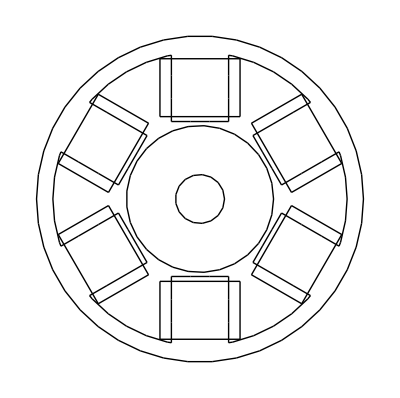

```mathematica
bMotorMesh=BoundaryElementMeshJoin[RegionUnion[Annulus[{0,0},{outerDiameter-outerShellThickness,outerDiameter}],Annulus[{0,0},{rotorInnerDiameter,rotorOuterDiameter}],Sequence@@Table[RotationTransform[x,{0,0}][Rectangle[{rotorOuterDiameter+rotorStatorDistance,-coilInnerDiameter/2},{outerDiameter-outerShellThickness,coilInnerDiameter/2}]],{x,(2 π)/numCoils*offsetCoils,2 π-(2 π)/numCoils(-offsetCoils+1),(2 π)/numCoils}]]//BoundaryDiscretizeRegion//ToBoundaryMesh,ToBoundaryMesh[BoundaryDiscretizeRegion[RegionUnion@@Table[RotationTransform[x,{0,0}][Rectangle[{rotorOuterDiameter+rotorStatorDistance+coilInnerOffset,-coilOuterDiameter/2},{outerDiameter-outerShellThickness-coilOuterOffset,coilOuterDiameter/2}]],{x,(2 π)/numCoils*offsetCoils,2 π-(2 π)/numCoils(-offsetCoils+1),(2 π)/numCoils}]]]];
bMotorMesh["Wireframe"]
```

```mathematica
markList[m_][{x_,y_}]:={{x,y},m}
{air,rotor,stator}=Range[0,2];
```

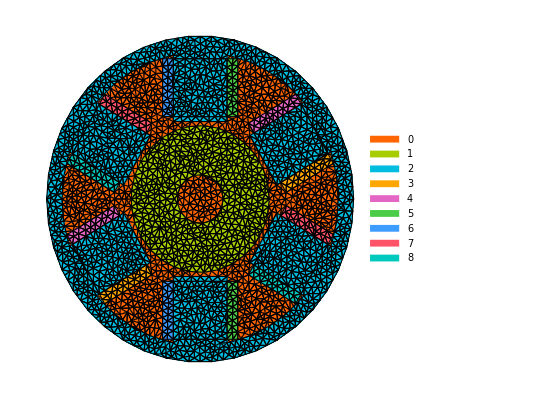

```mathematica
Clear[x,n]
statorSpec=markList[stator]/@Flatten[{Table[RotationTransform[x,{0,0}][{rotorOuterDiameter+rotorStatorDistance+outerDiameter-outerShellThickness,0}/2],{x,(2 π)/numCoils*offsetCoils,2 π-(2 π)/numCoils*(-offsetCoils+1),(2 π)/numCoils}],Table[RotationTransform[x,{0,0}][{rotorOuterDiameter+rotorStatorDistance+coilInnerOffset/2,0}],{x,(2 π)/numCoils*offsetCoils,2 π-(2 π)/numCoils(-offsetCoils+1),(2 π)/numCoils}],{{outerDiameter-outerShellThickness/2,0}}},1];
rotorSpec={{{rotorOuterDiameter/2+rotorInnerDiameter/2,0},rotor}};
airSpec={{{0,0},air},{{rotorOuterDiameter+rotorStatorDistance/2,0},air}};
coilSpec=Join@@Table[{{RotationTransform[x,{0,0}]@{((rotorOuterDiameter+rotorStatorDistance+coilInnerOffset)+(outerDiameter-outerShellThickness-coilOuterOffset))/2,(-coilInnerDiameter-coilOuterDiameter)/4},Piecewise[{{2+n,n≤numCoils}},(2+n)-numCoils+If[Mod[n,2]==1,1,-1]]/.n->(2(x-(2 π)/numCoils*offsetCoils)*numCoils/(2*Pi)+1)},{RotationTransform[x,{0,0}]@{((rotorOuterDiameter+rotorStatorDistance+coilInnerOffset)+(outerDiameter-outerShellThickness-coilOuterOffset))/2,(coilInnerDiameter+coilOuterDiameter)/4},Piecewise[{{2+n,n≤numCoils}},(2+n)-numCoils+If[Mod[n,2]==1,1,-1]]/.n->(2(x-(2 π)/numCoils*offsetCoils)*numCoils/(2*Pi)+2)}},{x,(2 π)/numCoils*offsetCoils,2 π-(2 π)/numCoils(-offsetCoils+1),(2 π)/numCoils}];
spec=Join[statorSpec,airSpec,rotorSpec,coilSpec];
MotorMesh=ToElementMesh[bMotorMesh,"RegionMarker"->spec,"ElementMeshGenerator"->"Continutity",MeshQualityGoal->.3,MaxCellMeasure->.00001,"NodeReordering"->True,"MeshOrder"->1];
MeshInspect[MotorMesh]
```

```mathematica
poles=2;
offset=1;
magnet=Graphics@Table[{FaceForm[{Red//Lighter,Blue//Lighter}[[Mod[x+1,2]+1]]],Annulus[{0,0},{rotorInnerDiameter,rotorOuterDiameter},{2*Pi/poles(x+offset),2*Pi/poles(x+offset)+2*Pi/poles}]},{x,0,poles}]
```

-Graphics-

```mathematica
Show[magnet,bMotorMesh["Wireframe"]]
```

-Graphics-

```mathematica
virtualCoilSize=.8/100;
magnetCurrentDensity=500000/virtualCoilSize;
magnetCurrent=SquareWave[poles*(t/(4*Pi))-1/4-offset/(2)] *Piecewise[{{magnetCurrentDensity,rotorInnerDiameter≤r≤rotorInnerDiameter+virtualCoilSize},{-magnetCurrentDensity,rotorOuterDiameter-virtualCoilSize≤r≤rotorOuterDiameter}},0]/.{r->Sqrt[x^2+y^2],t->ArcTan[x,y]}
DensityPlot[magnetCurrent,{x,y}∈Annulus[{0,0},{rotorInnerDiameter,rotorOuterDiameter}],PlotLegends->Automatic]
```

(Piecewise[{{6.25×10^7, 0.015≤√(x^2+y^2)≤0.023}, {-6.25×10^7, 0.037≤√(x^2+y^2)≤0.045}, {0, True}}]) SquareWave[1/4+ArcTan[x,y]/(2 π)]

```mathematica
SquareWave[x]//PiecewiseExpand
```

Piecewise[{{-1, 1/2≤Mod[x,1]<1}, {1, True}}]

```mathematica
MeshInspect[MotorMesh]
```

-Graphics-

```mathematica
current/((1.*^-3)^2*Pi)(coilOuterDiameter-coilInnerDiameter)*((outerDiameter-outerShellThickness-coilOuterOffset)-(rotorOuterDiameter+rotorStatorDistance+coilInnerOffset))
```

3164.

```mathematica
current=20;(* in A *)
wireDiameter=1.*^-3;
{in,out}={-1,1};
activeCoils={{1,out},{3,in}};
coilMarkers=ArrayReshape[Range[3,numCoils+3-1],{numCoils-1,2}];
coilCurrents=Flatten[Table[{coilMarkers[[i//First]],{-1,1}*(i//Last)}//Transpose,{i,activeCoils}],1];
coilCurrentDensity=current/((wireDiameter/2)^2*Pi);
coilFunction = Piecewise[Table[{coilCurrentDensity*Last[x],ElementMarker==First[x]},{x,coilCurrents}],0]//Simplify
```

Piecewise[{{-2.54648×10^7, ElementMarker==3||ElementMarker==8}, {2.54648×10^7, ElementMarker==4||ElementMarker==7}, {0, True}}]

```mathematica
fitData={Subscript[a, 0]->0.000037955129560483474,Subscript[a, 1]->0.00006575078254916768,Subscript[a, 2]->-0.000019250684240476186,Subscript[a, 3]->0.0002769129642720887,Subscript[a, 4]->-0.00040922344805632805,Subscript[a, 5]->0.0002096110387525365,Subscript[a, 6]->-0.00003809378487585398};
mu=Function[x,Evaluate[∑_(i=0)^6 Subscript[a, i] x^i/.fitData]]
```

Function[x,0.0000379551+0.0000657508 x-0.0000192507 x^2+0.000276913 x^3-0.000409223 x^4+0.000209611 x^5-0.0000380938 x^6]

```mathematica
mu2=Function[x,-0.0005066496325619219 ⅇ^(-42.077372984456105 (0.04885906655766546+x)^2)+0.007786216888333133/((1+ⅇ^(1.4181115724710933 (-0.7754925571416307+x)^2))^2)];
```

```mathematica
B2Norm=Sqrt@Total[Grad[a[x,y],{x,y}]^2+$MachineEpsilon];
```

```mathematica
Subscript[μ, 0]=4 π*10^-7;
```

```mathematica
ν=IdentityMatrix[2]*Piecewise[{{1/(1.05*Subscript[μ, 0]),ElementMarker==rotor},{1/(300*Subscript[μ, 0]),ElementMarker==stator}},1/Subscript[μ, 0]];
```

```mathematica
AbsoluteTiming[A=NDSolveValue[{Inactive[Div][Inactive[Dot][ν,Inactive[Grad][a[x,y],{x,y}]],{x,y}]==magnetCurrent+coilFunction,DirichletCondition[a[x,y]==0,x^2+y^2≥((outerDiameter-outerShellThickness/2))^2]},a,{x,y}∈MotorMesh]]
{min,max}=MinMax[A["ValuesOnGrid"]]
```

{0.139965,InterpolatingFunction[…]}

{-0.0215924,0.0370183}

```mathematica
potential=Show[ContourPlot[A[x,y],{x,y}∈MotorMesh,PlotRange->Full,Contours->Range[min,max,(max-min)/15],PlotLabel->Style[StringForm["Potential and Flux Inside a `` Coil `` Pole BLDC Motor: ``",numCoils,poles,If[current==0,"Unloaded",StringForm["Load Current `` A",current]]],FontSize->16],PlotTheme->"Scientific",ColorFunction->"TemperatureMap",LabelStyle->{FontFamily->"CMU Serif",FontColor->Black,FontSize->14},PlotLegends->BarLegend[Automatic,LegendLabel->Placed[Rotate["Magnetic Potential [T·m]",Pi/2],Right],LegendMarkerSize->500]],StreamPlot[Curl[A[x,y],{x,y}]//Evaluate,{x,y}∈MotorMesh,StreamPoints->Fine,StreamColorFunction->"Rainbow"],Graphics@Table[{FaceForm[{Opacity[.3],{Red//Lighter,Blue//Lighter}[[Mod[x+1,2]+1]]}],Annulus[{0,0},{rotorInnerDiameter,rotorOuterDiameter},{2*Pi/poles(x+offset),2*Pi/poles(x+offset)+2*Pi/poles}]},{x,0,poles}],bMotorMesh["Wireframe"],ImageSize->600,FrameLabel->{"[m]","[m]"},LabelStyle->{FontFamily->"CMU Serif",FontColor->Black,FontSize->14}]
```

-Graphics-

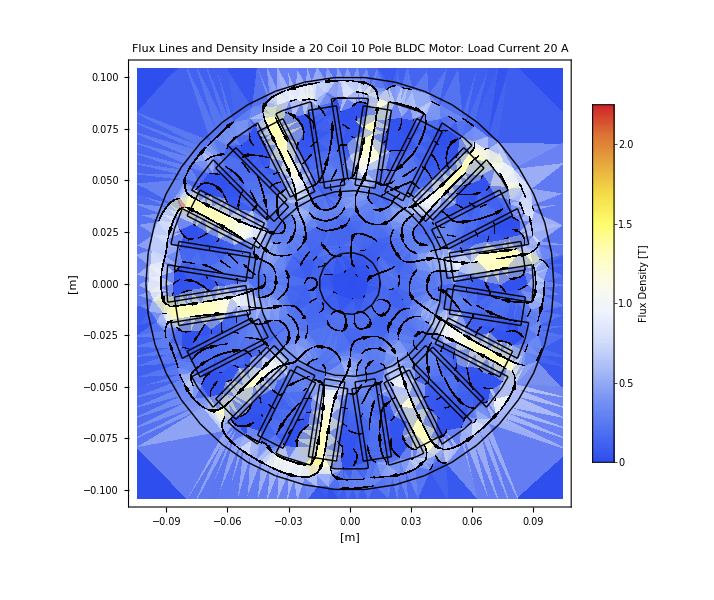

```mathematica
fluxDensity=Show[StreamDensityPlot[Curl[A[x,y],{x,y}]//Evaluate,{x,y}∈MotorMesh,StreamPoints->Fine,ColorFunction->"TemperatureMap",PlotTheme->"Scientific",PlotRange->Full,PlotLabel->Style[StringForm["Flux Lines and Density Inside a `` Coil `` Pole BLDC Motor: ``",numCoils,poles,If[current==0,"Unloaded",StringForm["Load Current `` A",current]]],FontSize->16],ColorFunctionScaling->True,LabelStyle->{FontFamily->"CMU Serif",FontColor->Black,FontSize->14},StreamMarkers->"PinDart",StreamColorFunction->Function[x,Black],PlotLegends->BarLegend[Automatic,LegendLabel->Placed[Rotate["Flux Density [T]",Pi/2],Right],LegendMarkerSize->500]],bMotorMesh["Wireframe"],ImageSize->600,FrameLabel->{"[m]","[m]"},LabelStyle->{FontFamily->"CMU Serif",FontColor->Black,FontSize->14}]
```

```mathematica
Export[ToString@StringForm["~/Desktop/potential-loaded-``coils.pdf",numCoils],potential]
Export[ToString@StringForm["~/Desktop/flux-loaded-``coils.pdf",numCoils],fluxDensity]
```

~/Desktop/potential-loaded-20coils.pdf

~/Desktop/flux-loaded-20coils.pdf

```mathematica
SystemOpen["~/Desktop/potential-loaded-6pole.pdf"]
```

```mathematica
GraphicsRow[{potential,fluxDensity},ImageSize->Full]
```

-Graphics-

```mathematica
τ=NIntegrate[(r^2 Evaluate[Fold[Times,TransformedField["Cartesian"->"Polar",-A[x,y]{x,y},{x,y}->{r,θ}]]])/Subscript[μ, 0],{r,rotorOuterDiameter,rotorStatorDistance+rotorOuterDiameter},{θ,0,2 π}]/rotorStatorDistance
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000817998 and 0.000200838 for the integral and error estimates.

-0.327199

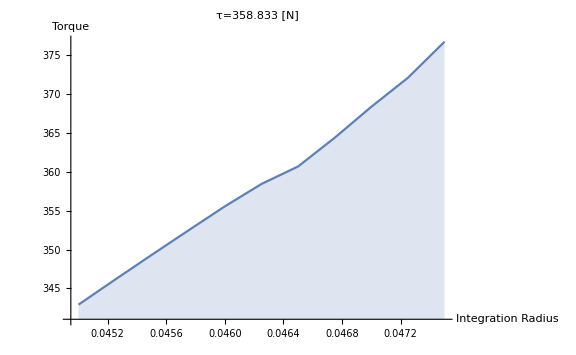

```mathematica
torque=ListLinePlot[#,PlotLabel->Style[StringForm["τ=`` [N]",Mean[#[[;;,2]]]],FontSize->16],LabelStyle->{FontFamily->"CMU Serif",FontColor->Black,FontSize->14},AxesLabel->{"Integration Radius","Torque"},ImageSize->Large,Filling->Axis]&@(Table[{s,-Quiet@NIntegrate[r^2*Evaluate[Fold[Times,TransformedField["Cartesian"->"Polar",-Curl[A[x,y],{x,y}],{x,y}->{r,θ}]]]/.r->s,{θ,0,2*Pi},Method->"LocalAdaptive"]/Subscript[μ, 0]},{s,Subdivide[rotorOuterDiameter,rotorOuterDiameter+rotorStatorDistance,10]}])
```

```mathematica
Export["~/Desktop/torque-20.pdf",torque]
```

~/Desktop/torque-20.pdf

```mathematica
SystemOpen["~/Desktop/torque1.pdf"]
```